# Mathematica Notebook for Finding Critical Values of λ

Here is my actual code that I actually ran to get my thesis data. For easier data collection, this was run as a loop once all the bugs were worked out. I present here the expanded version, which can be compressed and looped if desired.

## Finding candidate ranges

### Setup

```mathematica
l=0; (*Angular momentum quantum number*)
```

```mathematica
RoughCritical[λ_]:=Module[{H,res,dρ,ρinf,nn},
dρ=0.1;
ρinf=Round[20*λ];
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l*(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-100]];
Return[res]
]
```

This function takes a value of lambda and returns the 100 eigenvalues of the hamiltonian which have the lowest absolute value. nn is the matrix size, dρ is the step size, and ρinf is numerical infinity for the problem.

The results of this calculation are extremely sensitive to ρinf, and a larger ρinf makes for less error. However, for larger values of ρinf, more positive eigenvalues are found near 0, because the positive eigenvalues are in a continuous spectrum. As the grid becomes a better approximation of reality, more of these are picked up. This squeezes the negative eigenvalues (whose spectrum starts near -1) out, especially at higher values of λ. In order to ensure that there are *some* negative eigenvalues, we therefore pin ρinf to some constant factor times λ.

This is the actual function that was bisected -- it reports the number of negative numbers in a list, which in this case is a list of eigenvalues. A new negative eigenvalue corresponds to a new bound state.

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

#### Old

```mathematica
FindLs[l0_,lf_,val_,vaf_,range_]:=Module[{mid,vam,lnegs,mnegs,hnegs,res},
res={};
mid=l0+(lf-l0)/2;
lnegs=CountNegs[val];
vam=RoughCritical[mid];
mnegs=CountNegs[vam];
hnegs=CountNegs[vaf];
If[lf-l0>range,
If[lnegs<mnegs ||(lnegs==mnegs && val[[1]] < vam[[1]]&& mnegs>0),
res=Join[res,FindLs[l0,mid,val,vam,range]];
Return[res]
];
If[mnegs<hnegs || (hnegs==mnegs && vam[[1]] < vaf[[1]]&&hnegs>0),
res=Join[res,FindLs[mid,lf,vam,vaf,range]];
Return[res]
];
,
Print["Found one!"]; (*this lets you know it's working*)
Return[{{l0,lf}}];
]
]
```

This is my multiple rootfinder, to find ranges where a zero occurs. Again, when we bisect, we are looking at the number of negative eigenvalues as a function of lambda. In this routine, we assume multiple zeroes, and keep bisecting any range with a zero in it.

The complicated conditional for bisection is meant to deal with the problem of negative eigenvalues getting squeezed out by positive ones. Given a half of the input range, it bisects that half if either the number of negative eigenvalues increases (a regular zero), or the number of negative eigenvalues stays constant, but the value of the first negative eigenvalue jumps. This indicates that one negative eigenvalue was squeezed out, but another was added. In general, as λ increases, the negative eigenvalues should decrease in value (coming closer and closer to the Coulomb energies).

```mathematica
RangeChunk[low_,high_]:=Module[{res,val,vaf,lnegs,hnegs},
res={};
val=RoughCritical[low];
lnegs=CountNegs[val];
vaf=RoughCritical[high];
hnegs=CountNegs[vaf];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]] < vaf[[1]]&& hnegs>0),
res=FindLs[low,high,val,vaf,1];
];
Return[res]
]
```

### Calculation

Here the parallelization starts. All of those calls to Eigenvalues aren’t cheap, and the range-finding can be paralellized as well as the actual bisection calculation. RangeChunk, above, is just a wrapper for the function that finds ranges. It does the initial calculation and makes sure there’s a zero inside the the range before sending it off to be bisected.

```mathematica
NoKernels=21; (*Number of kernels in the Lightweight Grid*)
```

```mathematica
int=(5.*10^5-0.25/2)/NoKernels
```

```mathematica
chunks={{0.5,Sqrt[2*int+0.25]}}
For[i=1,i<NoKernels,i++,
chunks=Append[chunks,{chunks[[i,2]],Sqrt[chunks[[i,2]]^2+2*int]}]
]
```

The range -- λ = 0.5 to 1000 -- gets divided up based on the length of time it takes to run Eigenvalues there. The timing of Eigenvalues is roughly linear with ρinf. The amount of time it takes to find a range will therefore be approximately the integral of this line over the range.

```mathematica
DistributeDefinitions[RangeChunk,CountNegs,chunks,FindLs,RoughCritical,l] (*Every kernel needs all of the functions and lists being used*)
```

```mathematica
rangesrough=ParallelTable[RangeChunk[chunks[[i,1]],chunks[[i,2]]],{i,1,Length[chunks]}];
```

This comes out as a list of lists of pairs, and we just want a list of pairs. So we massage it a little.

```mathematica
ranges={};
```

```mathematica
For[i=1,i<Length[rangesrough],i++,
ranges=Join[ranges,rangesrough[[i]]];
]
```

## Rootfinding for Lcs

### Setup

```mathematica
MakeGrid[Δρ1_,Δρ2_,ρ0_,ρinf_]:=Module[{i,grid,lo,hi},
grid={};
i=0;(*here i is playing the role of ρ*)
While[i<ρinf,
lo=.5Δρ2 Tanh[(i-ρ0)/100]+.5Δρ2+Δρ1;(*Subscript[ρ, n]-Subscript[ρ, n-1]*)
i=i+.5Δρ2 Tanh[(i-ρ0)/100]+.5Δρ2+Δρ1;(*ρ, updated*)
hi=.5Δρ2 Tanh[(i-ρ0)/100]+.5Δρ2+Δρ1;(*Subscript[ρ, n+1]-Subscript[ρ, n]*)
grid=Append[grid,{lo,i,hi}];
];
Return[grid]
]
```

```mathematica
Critical[λ_,consts_]:=Module[{H,res,ρs,nn,a,b,rho},
ρs=MakeGrid[consts[[1]],consts[[2]],consts[[3]],consts[[4]]];
nn=Length[ρs];
a[n_]:=ρs[[n,1]];
b[n_]:=ρs[[n,3]];
rho[n_]:=ρs[[n,2]];
H=SparseArray[{{n_,n_}->4./(a[n]^2+b[n]^2)-2./rho[n] ⅇ^(-rho[n]/λ)+(l*(l+1))/(rho[n])^2,{n_, m_}/; Abs[n-m] == 1 -> -2./(a[n]^2+b[n]^2)},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-50]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

This is another version of the RoughCritical function above that only takes the 25 eigenvalues closest to 0. It also allows dρ and ρinf to be varied. Decreasing the number of eigenvalues taken sped up the calculation a lot, and if on every range we have 0 eigenvalues at the lower end and 1 on the upper end, that’s no big deal -- that’s still a negative eigenvalue appearing.

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]]; (*Again, lets you know it's working/progress*)
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];Par
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

Bisection rootfinder, finding where a new negative eigenvalue appears. It returns not only the midpoint, but the number of negative eigenvalues at the low and high ends of the final range. This allows for a quick eyeball check if necessary to verify that there is in fact a zero where the function says there is.

```mathematica
Findlc[input_,i_,eps_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[i]<>"th lambda, part "<>ToString[input[[1]]]];
res={input[[1]],Bisect[Critical,{input[[2,1]],input[[2,2]]},input[[3]],input[[4]],eps]};
Return[res]
]
```

This is the wrapper for parallel bisection. It makes sure that there is in fact a zero in the range, because the ρinf dependence means that sometimes the critical λ drifts out of the range. Any bisections done where there is no zero in the range would return the upper endpoint and be useless.

```mathematica
ListRandomize[list_]:=Module[{order,res},
order=Table[{RandomReal[],i},{i,1,Length[list]}];
order = Sort[order];
res=Table[list[[order[[i,2]]]],{i,1,Length[list]}];
Return[res]
]
```

This is a quick-and-dirty optimization for the parallel rootfinding. All it does is mix up the inputs so a kernel is less likely to get two long or two short calculations.

```mathematica
rhoinfs={40,80}; (*Scaling factors for λ*)
```

## Testing

```mathematica
SetDirectory["~/Library/AFS@Reed/emcmanis/Thesis/Calculations"]
```

/afs/reed.edu/user/e/m/emcmanis/Thesis/Calculations

```mathematica
l0 = Import["l0.csv"];
```

```mathematica
l0[[4]]
```

{12.6913,0.00346947}

```mathematica
range={l0[[4,1]]-0.25,l0[[4,1]]+0.25}
```

```mathematica
range={12.441329293329545,12.941329293329545}
```

{12.4413,12.9413}

```mathematica
?Bisect
```

Global`Bisect

Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},mid=x0+1/2 Abs[x0-xf];Print[Bisecting. Midpoint is <>ToString[mid]];val=F[x0,consts];lnegs=CountNegs[val];vam=F[mid,consts];mnegs=CountNegs[vam];If[xf-x0>ϵ,If[lnegs<mnegs||(lnegs==mnegs&&val⟦1⟧<vam⟦1⟧),Return[Bisect[F,consts,x0,mid,ϵ]];,Return[Bisect[F,consts,mid,xf,ϵ]];];,vah=F[xf,consts];Return[{mid,lnegs,CountNegs[vah]}];]]

```mathematica
consts={0.1,5,100,25000}
```

{0.1,5,100,25000}

```mathematica
ρs=MakeGrid[consts[[1]],consts[[2]],consts[[3]],consts[[4]]];
```

```mathematica
nn=Length[ρs];
```

```mathematica
l=0
```

0

```mathematica
λ=range[[1]];
```

```mathematica
a[n_]:=ρs[[n,1]];
b[n_]:=ρs[[n,3]];
rho[n_]:=ρs[[n,2]];
x[n_]:=5*n;
H=SparseArray[{{n_,n_}->4./(a[n]^2+b[n]^2)-2./rho[n] ⅇ^(-rho[n]/λ)+(l*(l+1))/(rho[n])^2,{n_, m_}/; Abs[n-m] == 1 -> -2./(a[n]^2+b[n]^2)},{nn,nn}, 0.];
```

Part::pspec: Part specification n is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

```mathematica
a[n_]:=ρs[[n,1]]
```

```mathematica
b[n_]:=ρs[[n,3]]
```

```mathematica
rho[n_]:=ρs[[n,2]]
```

```mathematica
H[[3,1;;4]]//MatrixForm
```

```mathematica
H[[1;;5,1;;5]]
```

SparseArray[<13>,{5,5}]

```mathematica
Table[4./(a[n]^2+b[n]^2)-2./rho[n] ⅇ^(-rho[n]/λ)+(l*(l+1))/(rho[n])^2,{n,1,5}]
```

{180.16,190.159,193.492,195.158,196.158}

```mathematica
l=0;
```

```mathematica
evs=Timing[Table[Critical[i,consts][[1;;3]],{i,11,14,0.05}]];
```

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

```mathematica
11+40*0.05
```

13.

```mathematica
Length[evs[[2]]]
```

61

```mathematica
evs[[1]]/60
```

2.38343

```mathematica
?Timing
```

Timing[expr] evaluates expr, and returns a list of the time in seconds used, together with the result obtained.

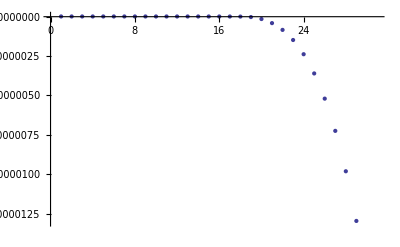

```mathematica
ListPlot[Table[evs[[2,i,1]],{i,10,40}]]
```

```mathematica
consts
```

{0.1,2,100,25000}

```mathematica
11+15*0.05
```

11.75

```mathematica
consts2={0.1,2,50,25000};
```

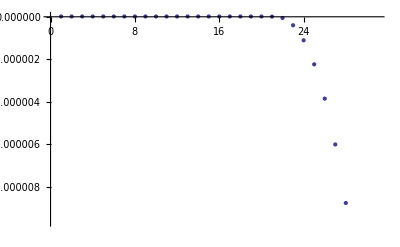

```mathematica
ListPlot[Table[evs2[[2,i,1]],{i,10,40}]]
```

```mathematica
evs2=Timing[Table[Critical[i,consts2][[1;;3]],{i,11,14,0.05}]];
```

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

```mathematica
low =Critical[λ,consts]
```

{{0.1,0.1,0.1},{0.1,0.2,0.1},{0.1,0.3,0.1}}

5375

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

{1.60616×10^-8,6.42462×10^-8,1.44552×10^-7,2.56978×10^-7,4.01522×10^-7,5.78178×10^-7,7.86945×10^-7,1.02782×10^-6,1.30079×10^-6,1.60585×10^-6,1.943×10^-6,2.31223×10^-6,2.71353×10^-6,3.1469×10^-6,3.61232×10^-6,4.10979×10^-6,4.6393×10^-6,5.20084×10^-6,5.7944×10^-6,6.41997×10^-6,7.07753×10^-6,7.76709×10^-6,8.48864×10^-6,9.24215×10^-6,0.0000100276}

```mathematica
CountNegs[low]
```

0

```mathematica
high=Critical[range[[2]],consts]
```

{{0.1,0.1,0.1},{0.1,0.2,0.1},{0.1,0.3,0.1}}

5375

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

{1.60238×10^-8,6.40951×10^-8,1.44213×10^-7,2.56377×10^-7,4.00585×10^-7,5.76835×10^-7,7.85125×10^-7,1.02545×10^-6,1.29781×10^-6,1.60221×10^-6,1.93862×10^-6,2.30706×10^-6,2.70752×10^-6,3.14×10^-6,3.60448×10^-6,4.10096×10^-6,4.62944×10^-6,5.18991×10^-6,5.78237×10^-6,6.40681×10^-6,7.06322×10^-6,7.7516×10^-6,8.47194×10^-6,9.22423×10^-6,0.0000100085}

```mathematica
low[[1]]-high[[1]]
```

0.000153716

```mathematica
CountNegs[high]
```

1

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]]; (*Again, lets you know it's working/progress*)
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
consts={0.1,2,100,25000}
```

{0.1,2,100,25000}

```mathematica
Timing[Bisect[Critical,consts,11.75,12.75,10^(-6)]]
```

Bisecting. Midpoint is 12.25

Part::pspec: Part specification n$ is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Bisecting. Midpoint is 12.5

Bisecting. Midpoint is 12.375

Bisecting. Midpoint is 12.3125

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.3281

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.3242

Bisecting. Midpoint is 12.3262

Bisecting. Midpoint is 12.3252

Bisecting. Midpoint is 12.3247

Bisecting. Midpoint is 12.3245

Bisecting. Midpoint is 12.3243

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

«5 more identical outputs»

{102.509,{12.3244,0,1}}

```mathematica
102.5/21
```

4.88095

## Old stuff

### First calculations: refinement

```mathematica
ranges={{0.84,0.845},{3.22,3.24},{7.109750866889954,7.22},{12.612077236175537,12.827343463897705},{19.672054767608643,19.95009756088257},{28.301846981048584,28.642311573028564},{38.50174379348755,38.904447078704834},{50.26915788650513,50.73803377151489},{63.60709619522095,64.141761302948},{78.5151047706604,79.11599397659302},{94.99402666091919,95.66045904159546},{113.04274606704712,113.77575731277466},{132.66100358963013,133.46212148666382},{153.848379611969,154.7197699546814},{176.60773706436157,177.5473256111145},{200.9363875389099,201.94617700576782},{226.8368363380432,227.91507291793823},{254.30670976638794,255.45525884628296},{283.346556186676,284.56644201278687},{313.9577269554138,315.2480025291443},{346.1389317512512,347.5005784034729},{379.8906750679016,381.32391595840454},{415.21240758895874,416.71833848953247},{452.1055417060852,453.68311834335327},{490.56863832473755,492.21898794174194},{530.6023898124695,532.3256268501282},{572.2062392234802,574.0033192634583},{615.3815493583679,617.251362323761},{661.,663.},{706.4430651664734,708.460343837738+0.5},{754.3291535377502-0.5,756.4213309288025+0.5},{803.7868390083313-1,805.9526534080505+1},{854.8145480155945-1,857.0550780296326+1},{907.412929058075-2,909.7282948493958+2},{961.5815386772156-2,963.9725241661072+2}}
```

To reduce the number of failed rootfinding attempts, we refined the rough ranges above a bit more at different values of ρinf. The first gets down to a range of width 1/4, the second, a range of width 1/32. The above ranges were entered when some data was retaken and have been left in if anyone wants to play with the code.

```mathematica
inputslow=Table[{i,{0.1,25000},ranges[[i,1]],ranges[[i,2]]},{i,1,Length[ranges]}];
```

In order to deal with randomization later, the inputs are tagged with a number so they can be sorted again. This number is retained by Findlc. 

This list is set up for a constant value of dρ and ρinf. This is how the l = 0 data was collected. The higher l data was collected using fixed values of dρ and values of ρinf equal to a scaling factor times λ.

```mathematica
inputslow=ListRandomize[inputslow];
```

```mathematica
DistributeDefinitions[Critical,Bisect,CountNegs,Findlc,FindlcTest,inputslow,l]
```

```mathematica
refinement=ParallelTable[Findlc[inputslow[[i]],i,0.25],{i,1,Length[inputslow]}]
```

```mathematica
refinement=Sort[refinement];
```

```mathematica
rangeshi=ranges;
```

```mathematica
inputshigh=Table[{i,{0.05,50000},rangeshi[[i,1]],rangeshi[[i,2]]},{i,1,Length[ranges]}];
```

```mathematica
DistributeDefinitions[inputshigh]
```

```mathematica
refinement={{3,{ranges[[1,1]],2}}};
```

```mathematica
inputshigh=ListRandomize[inputshigh]
```

```mathematica
DistributeDefinitions[inputshigh]
```

```mathematica
refinement2=ParallelTable[Findlc[inputshigh[[i]],i,1/32.],{i,1,Length[inputshigh]}]
```

```mathematica
refinement2=Sort[refinement2];
```

### Second calculation: lcs for real

```mathematica
ref1ins= Table[{i,rhoinfs[[1]]*refinement[[i,2,1]],refinement[[i,2,1]]-1.,refinement[[i,2,1]]+1.},{i,1,Length[refinement]}];
```

```mathematica
ref2ins=Table[{i+Length[ref1ins],rhoinfs[[2]]*refinement2[[i,2,1]],refinement2[[i,2,1]]-1.,refinement2[[i,2,1]]+1.},{i,1,Length[refinement2]}];
```

And now we combine the refined ranges, make input lists out of them, and find the values of the λcs to within 10^-6.

```mathematica
newins=Join[ref1ins,ref2ins];
```

```mathematica
newins=ListRandomize[newins];
```

```mathematica
DistributeDefinitions[newins,Findlc]
```

```mathematica
lcs=ParallelTable[Findlc[newins[[i]],i,10^-6],{i,1,Length[newins]}]
```

```mathematica
lcs=Sort[lcs]
```

{{1,{0.840619,0,1}},{1,{0.842713,0,1}},{2,{3.2245,0,1}},{2,{3.2268,0,1}},{3,{7.17228,0,1}},{3,{7.17497,0,1}},{4,{12.6879,0,1}},{4,{12.6913,0,1}},{5,{19.7727,0,1}},{5,{19.7775,0,1}},{6,{28.4277,0,1}},{6,{28.4344,0,1}},{7,{38.6532,0,1}},{7,{38.6626,0,1}},{8,{50.4496,0,1}},{8,{50.4627,0,1}},{9,{63.8173,0,1}},{9,{63.8351,0,1}},{10,{78.7564,0,1}},{10,{78.7803,0,1}},{11,{95.2673,0,1}},{11,{95.2986,0,1}},{12,{113.35,0,1}},{12,{113.39,0,1}},{13,{133.005,0,1}},{13,{133.056,0,1}},{14,{154.232,0,1}},{14,{154.296,0,1}},{15,{177.032,0,1}},{15,{177.111,0,1}},{16,{201.404,0,1}},{16,{201.501,0,1}},{17,{227.349,0,1}},{17,{227.466,0,1}},{18,{254.868,0,1}},{18,{255.008,0,1}},{19,{283.96,0,1}},{19,{284.126,0,1}},{20,{314.625,0,1}},{20,{314.821,0,1}},{21,{346.863,0,1}},{21,{347.094,0,1}},{22,{380.676,0,1}},{22,{380.945,1,2}},{23,{416.063,0,1}},{23,{416.374,1,2}},{24,{453.024,0,1}},{24,{453.384,1,2}},{25,{491.56,0,1}},{25,{491.974,1,2}},{26,{531.671,0,1}},{26,{532.145,1,2}},{27,{573.357,0,1}},{27,{573.898,1,2}},{28,{616.618,0,1}},{28,{617.235,1,2}},{29,{661.455,0,1}},{29,{1388640275/2097152,1,2}},{30,{707.868,0,1}},{30,{708.661,1,2}},{31,{755.858,1,2}},{31,{756.755,1,2}},{32,{805.424,1,2}},{32,{806.436,2,3}},{33,{856.567,1,2}},{33,{857.707,2,3}},{34,{909.288,1,2}},{34,{910.571,2,3}},{35,{963.587,1,2}},{35,{965.028,2,3}}}

Data again retained if anyone wants to play with it.

## Data Export

```mathematica
data=Table[{lcs[[i,2,1]],lcs[[i-Length[lcs]/2,2,1]]-lcs[[i,2,1]]},{i,Length[lcs]/2+1,Length[lcs]}];
```

This bit exports the data to a file for further analysis. The directory should be set to wherever this notebook is running.

As discussed in the thesis, the data is in the form {data, error}, where the error is found by calculating the difference in λ_n when ρinf  and/or dρ is varied.

```mathematica
SetDirectory["~/Thesis/Calculations/"]
```

```mathematica
Export["l"<>ToString[l]<>".csv",data]
```

l0.csv